Solving an ODE (§5):

```mathematica
Quit[]
```

```mathematica
D[z[t],t]==a*z[t]
```

z'[t]==a z[t]

```mathematica
DSolveValue[D[z[t],t]==a*z[t],z[t],t]
```

ⅇ^(a t) C[1]

```mathematica
DSolveValue[{D[z[t],t]==a*z[t],z[0]==z0},z[t],t]
```

ⅇ^(a t) z0

```mathematica
z'[t]==a *z[t]
```

z'[t]==a z[t]

```mathematica
DSolveValue[z'[t]==a*z[t],z[t],t]
```

ⅇ^(a t) C[1]

```mathematica
DSolveValue[{z'[t]==a*z[t],z[0]==z0},z[t],t]
```

ⅇ^(a t) z0

```mathematica
ode=D[z[t],t]==a*z[t]
init=z[0]==z0
DSolveValue[ode,z[t],t]
sol=DSolveValue[{ode,init},z[t],t]
sol/.t->3
zsol=sol
```

z'[t]==a z[t]

z[0]==z0

ⅇ^(a t) C[1]

ⅇ^(a t) z0

ⅇ^(3 a) z0

ⅇ^(a t) z0

```mathematica
a=-Log[2]/14
sol
sol/.{z0->1,t->60}
N[%]
```

-Log[2]/14

2^(-t/14) z0

1/(16 2^(2/7))

0.051271

```mathematica
sol
Values[NSolve[sol==0.5*z0,t]]
D[sol,t]
```

2^(-t/14) z0

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{14.}}

-1/7 2^(-1-t/14) z0 Log[2]

```mathematica
Quit[]
```

```mathematica
DSolveValue[{D[z[t],t]==z[t]*t,z[0]==3},z[t],t]
```

3 ⅇ^(t^2/2)

```mathematica
ode=D[z[t],t]==z[t]*t
init=z[0]==3
sol=DSolveValue[{ode,init},z[t],t]
```

z'[t]==t z[t]

z[0]==3

3 ⅇ^(t^2/2)

```mathematica
Quit[]
```

```mathematica
logistEq=D[n[t],t]==r*n[t]*(1-n[t]/K)
init=n[0]==N0
logistSol=DSolveValue[{logistEq,init},n[t],t]
```

n'[t]==r n[t] (1-n[t]/K)

n[0]==N0

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(ⅇ^(r t) K N0)/(K-N0+ⅇ^(r t) N0)

```mathematica
Quit[]
```

```mathematica
DSolveValue[{D[z[t],t]==z[t]+t,z[0]==z0},z[t],t]
```

-1+ⅇ^t-t+ⅇ^t z0

```mathematica
Quit[]
```

```mathematica
DSolveValue[{D[z[t],t]==z[t]^2+t,z[0]==z0},z[t],t]
```

(-2 t^(3/2) z0 BesselJ[-2/3,(2 t^(3/2))/3] Gamma[1/3]+3^(1/3) t^(3/2) BesselJ[-4/3,(2 t^(3/2))/3] Gamma[2/3]+3^(1/3) BesselJ[-1/3,(2 t^(3/2))/3] Gamma[2/3]-3^(1/3) t^(3/2) BesselJ[2/3,(2 t^(3/2))/3] Gamma[2/3])/(2 t (z0 BesselJ[1/3,(2 t^(3/2))/3] Gamma[1/3]-3^(1/3) BesselJ[-1/3,(2 t^(3/2))/3] Gamma[2/3]))

```mathematica
ode=D[z[t],t]==Log[z[t]]+t
init=z[0]==z0
sol=DSolveValue[{ode,init},z[t],t]
```

z'[t]==t+Log[z[t]]

z[0]==z0

DSolveValue[{z'[t]==t+Log[z[t]],z[0]==z0},z[t],t]

z'[t]==-0.1 z[t]

z[0]==3

InterpolatingFunction[{{0., 50.}}, <>][t]

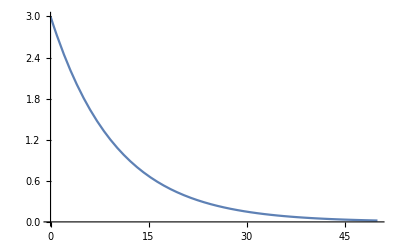

```mathematica
ode=D[z[t],t]==-0.1*z[t]
init=z[0]==3
sol=NDSolveValue[{ode,init},z[t],{t,0,50}]
Plot[sol,{t,0,50}]
```

z'[t]==t+Log[z[t]]

InterpolatingFunction[{{0., 10.}}, <>][t]

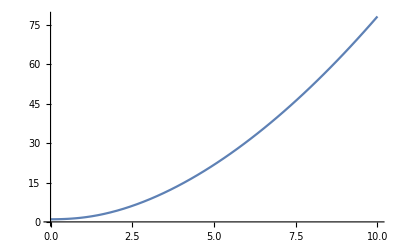

```mathematica
ode=D[z[t],t]==Log[z[t]]+t
sol=Nce[{ode,z[0]==1},z[t],{t,0,10}]
Plot[sol,{t,0,10}]
```

```mathematica
DSolveValue
```

```mathematica
f=z^3+3*z^2-2*z
ode=D[z[t],t]==f/.z->z[t]
```

-2 z+3 z^2+z^3

z[t]'[t]==-2 z[t]+3 z[t]^2+z[t]^3

```mathematica
Clear[f]
f[z_]=z^3+3*z^2-2*z
ode=D[z[t],t]==f[z[t]]
```

-2 z+3 z^2+z^3

z'[t]==-2 z[t]+3 z[t]^2+z[t]^3